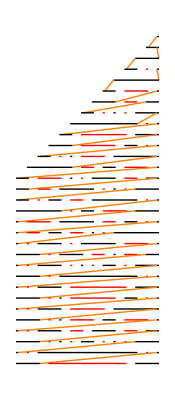

```mathematica
list = Table[0, {30}];
list[[15]] = 1;
rules = {
{0,0,0} -> 0,
{0,0,1} -> 1, 
{0,1,0} -> 1, 
{0,1,1} -> 1, 
{1,0,0} -> 0, 
{1,0,1} -> 1,
{1,1,0} -> 1,
{1,1,1} -> 0
};
(*Chop up the list and apply the rules*)
Partition[list, 3, 1] /. rules;
(*Pad the list with zeros on both sides*)
Join[{0}, list, {0}];
(*Create a function to do this*)
step[seq_] := Join[{0}, Partition[seq, 3, 1] /. rules, {0}];
array = NestList[step, list, 30];

summarizedArray = {};
padding = 0.1;
For[i = 1, i≤ Length[array], ++i,
	(* row i *)
	line = {};
	For[j=1, j≤ Length[array[[i]]], ++j,
		If[Length[line] == 0, (* init *)
			line = {i,j,i,j, array[[i,j]]}, 
		(*else: if value is the same as last line's value*)
			If[array[[i,j]] == line[[5]],
				line = {line[[1]], line[[2]], i,j, line[[5]]},
				(*else: new value --> store old line, start new line*)
				summarizedArray = Append[summarizedArray, line]; line = {i,j,i,j,array[[i,j]]}]
		]
	]
]
SubArrayToLine[a_] := (
	p1 = {a[[2]]-padding, -a[[1]]};
	p2 = {a[[4]]+padding, -a[[3]]};
	l = Line[{p1, p2}];
	Return[l];
)
FormattingOfLine[x_]:=(
	Return[ If[x == 0 , Red, If[x == 1, Black, Orange]]];
)

FormatRawLineList[x_]:=(
	formattedLines = {};
	For[k = 1, k ≤ Length[x],++k,
		formattedLines = Append[formattedLines, FormattingOfLine[x[[k,5]]]];
		formattedLines = Append[formattedLines, SubArrayToLine[x[[k]]]];
	];
	Return[formattedLines];
)

RemoveTrailingZeroLines[x_]:=(
	indicesToBeDropped = {};
	(*first element*)
	If[ x[[1,5]]==0 , indicesToBeDropped=Append[indicesToBeDropped, {1}], 0]
	(* rest *)
	For[i=2,i≤Length[x]-1,++i,
		(*look at neighbors left and right, same y value? *)
		If[    (x[[i,5]] == 0 && x[[i,1]] ≠ x[[i-1,1]])       (* is zero-line and leading *)
			|| (x[[i,5]] == 0 && x[[i,1]] ≠ x[[i+1,1]]),       (* is zero-line and trailing *)
			indicesToBeDropped=Append[indicesToBeDropped, {i}],
			0]
	]
	(* last element *)
	If[Last[x][[5]]==0 , indicesToBeDropped = Append[indicesToBeDropped,{Length[x]}], 0];
	Return[Delete[x, indicesToBeDropped]]
	
)

AddRowStraddlingLines[x_]:=(
	resultList = {};
	For[i=1,i≤Length[x]-1,++i,
		resultList = Append[resultList, x[[i]]];
		If[x[[i,1]] ≠ x[[i+1,1]] && x[[i,5]] == 1 && x[[i+1,5]] == 1,   (* next line has different y-value *)
			tmp = x[[i]];
			resultList = Append[resultList, GetStraddlingLine[x[[i]], x[[i+1]], i, 3]]
			(*resultList = Append[resultList, {tmp[[1]], tmp[[2]], x[[i+1,3]], x[[i+1,4]], 0}]*),
			0];
	]
	resultList = Append[resultList, Last[x]];
	Return[resultList]
)

GetStraddlingLine[x1_, x2_, i_, type_]:=(
	(*Alternate end-end / start-start
	tmp[[1]], tmp[[2]], x[[i+1,3]], x[[i+1,4]], 0} *)
	i1; i2; i3; i4;
	If[Mod[i,2]==0, i1 = 3, i1 = 1];
	If[Mod[i,2]==0, i2 = 4, i2 = 2];
	If[Mod[i,2]==0, i3 = 3, i3 = 1];
	If[Mod[i,2]==0, i4 = 4, i4 = 2];
	line = {x1[[i1]], x1[[i2]], x2[[i3]], x2[[i4]], type};
	Return[line]
)

(*formattedLines = FormatRawLineList[summarizedArray];
Graphics[{ Thick, formattedLines}]*)
trimmed = RemoveTrailingZeroLines[summarizedArray];
a = AddRowStraddlingLines[trimmed];
formatted = FormatRawLineList[a];
Graphics[{ Thick, formatted}]
ArrayPlot[array];
```